```mathematica
If[MatchQ[PacletInformation["QCDLib"], {}],
PacletInstall[URLDownload["https://scripts.mit.edu/~gurtej/mma_paclets/qcdlib.paclet"]]];
<<QCDLib`;
```

Loaded QCDLib`visualize` with symbols: {draw2DLogmags,draw2DPhases,draw2DResids,drawpath}

Loaded QCDLib`util` with symbols: {addQuad,arrayReshape,cache,cacheable,CacheDir,comm,coordMod,deepEq,dumpGlobalFns,exportRel,fname,getOptsFor,makeEvalSupp,mmaColors,mmaPlotMarkers,nanToZero,ones,readRel,relPath,symbolsWithDownValues,symmMat,wrap,writeRel}

Loaded QCDLib`plot` with symbols: {bigErrBarFn,constFitEpilog,errorListLogPlot,frameOpts,title}

Loaded QCDLib`analyze` with symbols: {autocorrs,bootstrap,constantFit,constantSysFit,getMeffs,meff,meffAcosh,stdDev}

Loaded QCDLib`sn` with symbols: {getCSCO,getCSCOSubspace,getTabxRep,getTabxShape,getTabxTabList,getYamanouchiSymbol,PermRep,regularTabxShapeQ,toGraphics,YoungTab,YoungTabx}

Loaded QCDLib`sun` with symbols: {gellMann,pauli,su2AdjGens,su2f,su2Gens,su3AdjGens,su3f,su3Gens}

Loaded QCDLib`phase` with symbols: {get2DResids}

```mathematica
ups[l_] := Table[0.75^(i), {i, 0, l-1}];
ps[l_] := Module[{out},
out = ups[l];
out / Total[out]
];
```

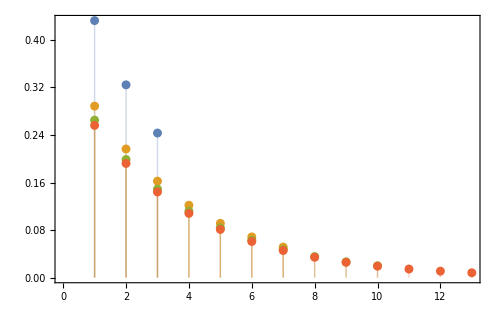

```mathematica
ListPlot[{ps[3], ps[7], ps[10], ps[13]}, Filling->Axis, frameOpts[]]
```

```mathematica
13!
```

6227020800

```mathematica
opts =Range[0, 12]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
maxOpt = Sum[i-1, {i, 13}]
```

78

```mathematica
{dists, allCounts} = Module[{weights, newWeights, weightsI, counts, newCounts, allCounts, i, j, dists},
weights = ReplacePart[ConstantArray[0, maxOpt], 1 -> 1.0];
counts = ReplacePart[ConstantArray[0, maxOpt], 1 -> 1];
dists = {};
allCounts = {};
For[i = 13, i ≥ 1, i--,
newWeights = ConstantArray[0, maxOpt];
newCounts = ConstantArray[0, maxOpt];
weightsI = ups[i];
For[j = 1, j ≤ Length[weightsI], j++,
newWeights += weightsI⟦j⟧  * RotateRight[weights, j-1];
newCounts += RotateRight[counts, j-1];
];
weights = newWeights;
counts = newCounts;
AppendTo[dists, weights / Total[weights]];
AppendTo[allCounts, counts];
];
{dists, allCounts}
];
```

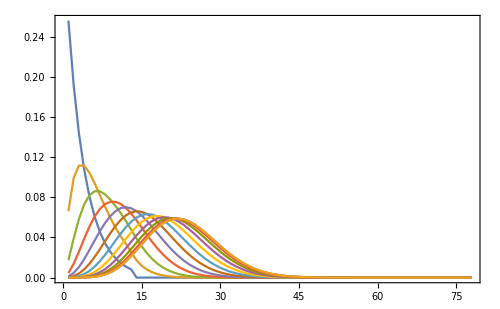

```mathematica
ListPlot[dists, Joined->True, PlotRange->All, frameOpts[]]
```

```mathematica
allCounts⟦-1⟧
```

{2,12,77,351,1274,3914,10569,25728,57486,119483,233389,431886,762007,1288587,2097472,3298033,5024460,7435284,10710609,15046642,20647290,27712842,36426054,46936280,59342609,73677240,89890517,107839121,127278852,147863220,169148705,190607064,211644496,231626875,249909685,265870800,278943900,288650143,294625748,296643390,294625748,288650143,278943900,265870800,249909685,231626875,211644496,190607064,169148705,147863220,127278852,107839121,89890517,73677240,59342609,46936280,36426054,27712842,20647290,15046642,10710609,7435284,5024460,3298033,2097472,1288587,762007,431886,233389,119483,57486,25728,10569,3914,1274,351,77,12}

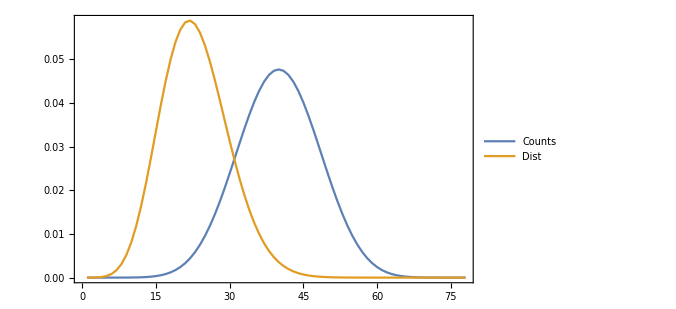

```mathematica
ListPlot[{allCounts⟦-1⟧/Total[allCounts⟦-1⟧], dists⟦-1⟧}, Joined->True, PlotRange->All, frameOpts[], PlotLegends->Placed[{"Counts", "Dist"}, {0.9, 0.9}]]
```

```mathematica
totCount = Total[allCounts⟦-1⟧]
```

6227020800

```mathematica
(* Good fidelity if we truncate above 45 *)
truncCDF = Total[dists⟦-1,;; 45⟧]
```

0.99852

```mathematica
truncCount = Total[allCounts⟦-1, ;; 45⟧]
truncFrac = N[truncCount / totCount];
Print["Still need to account for ", truncFrac, " frac."];
```

4639832372

Still need to account for 0.745113 frac.